# General assumptions

```mathematica
$Assumptions=Element[x,Reals] && x>0 && x<1 &&Element[y,Reals] && y>0 && y<1&&Element[z,Reals] && z>0 && z<1&&Element[zp,Reals] && zp>0 && zp<1
```

x∈ℝ&&x>0&&x<1&&y∈ℝ&&y>0&&y<1&&z∈ℝ&&z>0&&z<1&&zp∈ℝ&&zp>0&&zp<1

# Support

```mathematica
rho[x_,y_]=HeavisideTheta[1-x/y]HeavisideTheta[x/y]Sign[y]
```

HeavisideTheta[1-x/y] HeavisideTheta[x/y] Sign[y]

# Basic functions

```mathematica
F[x_,y_]=2CF(x/y)(1-1/(x-y))
G[x_,y_]=-4nf TR (x/y)(4(1-x)+(1-2x)/y)
H[x_,y_]=2CF(1-x^2/y)
Jr[x_,y_]=2CA(2(x^2/y)(3-2x+(1-x)/y)-(x+y)/y^2)
Js[x_,y_] = 2CA/(y-x)
```

(2 CF x (1-1/(x-y)))/y

-(4 nf TR x (4 (1-x)+(1-2 x)/y))/y

2 CF (1-x^2/y)

2 CA ((2 x^2 (3-2 x+(1-x)/y))/y-(x+y)/y^2)

(2 CA)/(-x+y)

# ERBL-form Kernels

```mathematica
Vqq0[x_,y_]=rho[x,y]F[x,y]+rho[1-x,1-y]F[1-x,1-y]
Vqg0[x_,y_]=((2y-1)/2)(rho[x,y]G[x,y]-rho[1-x,1-y]G[1-x,1-y])
Vgq0[x_,y_]=(2/(2x-1))(rho[x,y]H[x,y]-rho[1-x,1-y]H[1-x,1-y])
Vggr0[x_,y_]=((2y-1)/(2x-1))(rho[x,y]Jr[x,y]+rho[1-x,1-y]Jr[1-x,1-y])
Vggs0[x_,y_]=((2y-1)/(2x-1))(rho[x,y]Js[x,y]+rho[1-x,1-y]Js[1-x,1-y])
```

(2 CF (1-x) (1-1/(-x+y)) HeavisideTheta[1-(1-x)/(1-y)] HeavisideTheta[(1-x)/(1-y)] Sign[1-y])/(1-y)+(2 CF x (1-1/(x-y)) HeavisideTheta[1-x/y] HeavisideTheta[x/y] Sign[y])/y

1/2 (-1+2 y) ((4 nf TR (1-x) (4 x+(1-2 (1-x))/(1-y)) HeavisideTheta[1-(1-x)/(1-y)] HeavisideTheta[(1-x)/(1-y)] Sign[1-y])/(1-y)-(4 nf TR x (4 (1-x)+(1-2 x)/y) HeavisideTheta[1-x/y] HeavisideTheta[x/y] Sign[y])/y)

1/(-1+2 x)2 (-2 CF (1-(1-x)^2/(1-y)) HeavisideTheta[1-(1-x)/(1-y)] HeavisideTheta[(1-x)/(1-y)] Sign[1-y]+2 CF (1-x^2/y) HeavisideTheta[1-x/y] HeavisideTheta[x/y] Sign[y])

1/(-1+2 x)(-1+2 y) (2 CA ((2 (1-x)^2 (3-2 (1-x)+x/(1-y)))/(1-y)-(2-x-y)/(1-y)^2) HeavisideTheta[1-(1-x)/(1-y)] HeavisideTheta[(1-x)/(1-y)] Sign[1-y]+2 CA ((2 x^2 (3-2 x+(1-x)/y))/y-(x+y)/y^2) HeavisideTheta[1-x/y] HeavisideTheta[x/y] Sign[y])

((-1+2 y) ((2 CA HeavisideTheta[1-(1-x)/(1-y)] HeavisideTheta[(1-x)/(1-y)] Sign[1-y])/(x-y)+(2 CA HeavisideTheta[1-x/y] HeavisideTheta[x/y] Sign[y])/(-x+y)))/(-1+2 x)

# DGLAP - form kernels

```mathematica
Gammqq0[z_,zp_]=Vqq0[(1/2)(1+z),(1/2)(1+zp)]
Gammqg0[z_,zp_]=Vqg0[(1/2)(1+z),(1/2)(1+zp)]
Gammgq0[z_,zp_]=Vgq0[(1/2)(1+z),(1/2)(1+zp)]
Gammggr0[z_,zp_]=Vggr0[(1/2)(1+z),(1/2)(1+zp)]
Gammggs0[z_,zp_]=Vggs0[(1/2)(1+z),(1/2)(1+zp)]
```

(2 CF (1+1/2 (-1-z)) (1-1/(1/2 (-1-z)+(1+zp)/2)) HeavisideTheta[1-(1+1/2 (-1-z))/(1+1/2 (-1-zp))] HeavisideTheta[(1+1/2 (-1-z))/(1+1/2 (-1-zp))] Sign[1+1/2 (-1-zp)])/(1+1/2 (-1-zp))+(2 CF (1+z) (1-1/((1+z)/2+1/2 (-1-zp))) HeavisideTheta[(1+z)/(1+zp)] HeavisideTheta[1-(1+z)/(1+zp)] Sign[1+zp])/(1+zp)

1/2 zp (1/(1+1/2 (-1-zp))4 nf TR (1+1/2 (-1-z)) (2 (1+z)+(1-2 (1+1/2 (-1-z)))/(1+1/2 (-1-zp))) HeavisideTheta[1-(1+1/2 (-1-z))/(1+1/2 (-1-zp))] HeavisideTheta[(1+1/2 (-1-z))/(1+1/2 (-1-zp))] Sign[1+1/2 (-1-zp)]-(4 nf TR (1+z) (4 (1+1/2 (-1-z))-(2 z)/(1+zp)) HeavisideTheta[(1+z)/(1+zp)] HeavisideTheta[1-(1+z)/(1+zp)] Sign[1+zp])/(1+zp))

1/z 2 (-2 CF (1-(1+1/2 (-1-z))^2/(1+1/2 (-1-zp))) HeavisideTheta[1-(1+1/2 (-1-z))/(1+1/2 (-1-zp))] HeavisideTheta[(1+1/2 (-1-z))/(1+1/2 (-1-zp))] Sign[1+1/2 (-1-zp)]+2 CF (1-(1+z)^2/(2 (1+zp))) HeavisideTheta[(1+z)/(1+zp)] HeavisideTheta[1-(1+z)/(1+zp)] Sign[1+zp])

1/z zp (2 CA ((2 (1+1/2 (-1-z))^2 (3-2 (1+1/2 (-1-z))+(1+z)/(2 (1+1/2 (-1-zp)))))/(1+1/2 (-1-zp))-(2+1/2 (-1-z)+1/2 (-1-zp))/(1+1/2 (-1-zp))^2) HeavisideTheta[1-(1+1/2 (-1-z))/(1+1/2 (-1-zp))] HeavisideTheta[(1+1/2 (-1-z))/(1+1/2 (-1-zp))] Sign[1+1/2 (-1-zp)]+2 CA (((1+z)^2 (2-z+(2 (1+1/2 (-1-z)))/(1+zp)))/(1+zp)-(4 ((1+z)/2+(1+zp)/2))/(1+zp)^2) HeavisideTheta[(1+z)/(1+zp)] HeavisideTheta[1-(1+z)/(1+zp)] Sign[1+zp])

(zp ((2 CA HeavisideTheta[1-(1+1/2 (-1-z))/(1+1/2 (-1-zp))] HeavisideTheta[(1+1/2 (-1-z))/(1+1/2 (-1-zp))] Sign[1+1/2 (-1-zp)])/((1+z)/2+1/2 (-1-zp))+(2 CA HeavisideTheta[(1+z)/(1+zp)] HeavisideTheta[1-(1+z)/(1+zp)] Sign[1+zp])/(1/2 (-1-z)+(1+zp)/2)))/z

# DGLAP-regime region

```mathematica
$Assumptions=Join[$Assumptions && Element[kappa,Reals]&&kappa>-1&&kappa<1&&kappa≠0]
```

x∈ℝ&&x>0&&x<1&&y∈ℝ&&y>0&&y<1&&z∈ℝ&&z>0&&z<1&&zp∈ℝ&&zp>0&&zp<1&&kappa∈ℝ&&kappa>-1&&kappa<1&&kappa≠0

```mathematica
Pqq0DGLAP[kappa_,z_]=FullSimplify[Gammqq0[1/kappa,1/(kappa z)]/(2Abs[kappa] z)]
Pqg0DGLAP[kappa_,z_]=FullSimplify[Gammqg0[1/kappa,1/(kappa z)]/(2Abs[kappa] z)]
Pgq0DGLAP[kappa_,z_]=FullSimplify[Gammgq0[1/kappa,1/(kappa z)]/(2Abs[kappa] z)]
Pggr0DGLAP[kappa_,z_]=FullSimplify[Gammggr0[1/kappa,1/(kappa z)]/(2Abs[kappa] z)]
Pggs0DGLAP[kappa_,z_]=FullSimplify[Gammggs0[1/kappa,1/(kappa z)]/(2Abs[kappa] z)]
```

(2 CF (1+(1-2 kappa^2) z^2))/((-1+z) (-1+kappa^2 z^2))

-(4 nf TR (-1+z (2+(-2+kappa^2) z)))/((-1+kappa^2 z^2)^2)

(2 CF (-2+z (2+(-1+kappa^2) z)))/(z (-1+kappa^2 z^2))

(4 CA (-2+z (1-z+kappa^2 (1+z))))/((-1+kappa^2 z^2)^2)

(4 CA)/(z-z^2)

# Local terms

Pqq is already all plus-prescripted, therefore its local term is given by the negative of its integral between 0 and x .

```mathematica
Lqq0DGLAP[kappa_,x_]=TrigToExp[-Integrate[Pqq0DGLAP[kappa,y],{y,0,x}]]
```

4 CF Log[1-x]-(CF Log[1-kappa x])/kappa+(CF Log[1+kappa x])/kappa-(CF Log[1-kappa^2 x^2])/kappa^2

Pgg is not fully plus-prescripted. To avoid problems at x = 0, I decide to plus-prescribe all the regular part by a term 1/x.

```mathematica
Lgg0DGLAP[kappa_,x_]=TrigToExp[-Integrate[Pggr0DGLAP[kappa,y],{y,x,1}]]
```

-(2 CA (-((kappa+kappa^3) (-1+x))/(-1+kappa^2 x^2)+1/2 (1-3 kappa^2) (-Log[1-(kappa (-1+x))/(-1+kappa^2 x)]+Log[1+(kappa (-1+x))/(-1+kappa^2 x)])))/kappa^3

# DGLAP limit

```mathematica
Pqq0DGLAP[0,z]
Pqg0DGLAP[0,z]
Pgq0DGLAP[0,z]
Pggr0DGLAP[0,z]
Pggs0DGLAP[0,z]
```

-(2 CF (1+z^2))/(-1+z)

-4 nf TR (-1+(2-2 z) z)

-(2 CF (-2+(2-z) z))/z

4 CA (-2+(1-z) z)

(4 CA)/(z-z^2)

# DGLAP-ERBL transition point

```mathematica
FullSimplify[Pqq0DGLAP[1,z]]
FullSimplify[Pqg0DGLAP[1,z]]
FullSimplify[Pgq0DGLAP[1,z]]
FullSimplify[Pggr0DGLAP[1,z]]
FullSimplify[Pggs0DGLAP[1,z]]
FullSimplify[Lqq0DGLAP[1,z]]
FullSimplify[Lgg0DGLAP[1,z]]
```

-(2 CF)/(-1+z)

(4 nf TR)/(1+z)^2

(4 CF)/(z+z^2)

(8 CA)/((-1+z) (1+z)^2)

(4 CA)/(z-z^2)

2 CF Log[1-z]

CA ∞

# ERBL-regime region

```mathematica
$Assumptions=Element[x,Reals] && x>0 && x<1 &&Element[y,Reals] && y>0 && y<1&&Element[z,Reals] && z>0 && z<1&&Element[zp,Reals] && zp>0 && zp<1&&kappa>1&&kappa z≠1
```

x∈ℝ&&x>0&&x<1&&y∈ℝ&&y>0&&y<1&&z∈ℝ&&z>0&&z<1&&zp∈ℝ&&zp>0&&zp<1&&kappa>1&&kappa z≠1

```mathematica
Pqq0ERBL[kappa_,z_]=FullSimplify[Gammqq0[1/kappa,1/(kappa z)]/(2Abs[kappa] z)]
Pqg0ERBL[kappa_,z_]=FullSimplify[Gammqg0[1/kappa,1/(kappa z)]/(2Abs[kappa] z)]
Pgq0ERBL[kappa_,z_]=FullSimplify[Gammgq0[1/kappa,1/(kappa z)]/(2Abs[kappa] z)]
Pggr0ERBL[kappa_,z_]=FullSimplify[Gammggr0[1/kappa,1/(kappa z)]/(2Abs[kappa] z)]
Pggs0ERBL[kappa_,z_]=FullSimplify[Gammggs0[1/kappa,1/(kappa z)]/(2Abs[kappa] z)]
```

-(2 CF)/(-1+z)+(CF-CF kappa)/(kappa+kappa^2 z)

-(2 (1+kappa) nf TR (-1+kappa+(-2+kappa) kappa z))/(kappa^3 z (1+kappa z)^2)

(2 CF kappa+CF (-1+(-2+kappa) kappa) z)/(kappa z (1+kappa z))

(CA (-1+3 kappa^2-kappa (2+(-1+kappa)^2 kappa) z))/(kappa^3 z (1+kappa z)^2)

(2 CA)/(z-z^2)

# Local terms

```mathematica
Lgg0ERBL[kappa_]=FullSimplify[TrigToExp[Integrate[Pggr0ERBL[kappa,y]+2CA/y,{y,x,1}]]]
```

CA (-2 Log[x]+(((kappa+kappa^3) (-1+x))/(1+kappa x)+(1-3 kappa^2) Log[((1+kappa) x)/(1+kappa x)])/kappa^3)

# Limit at z = Infinity (relevant at x = 0)

```mathematica
FullSimplify[Limit[Pqq0ERBL[kappa,w]w,w->Infinity]]
FullSimplify[Limit[Pqg0ERBL[kappa,w]w,w->Infinity]]
FullSimplify[Limit[Pgq0ERBL[kappa,w]w,w->Infinity]]
FullSimplify[Limit[Pggr0ERBL[kappa,w]w+Pggs0ERBL[kappa,w]w,w->Infinity]]
```

-(CF (-1+kappa+2 kappa^2))/kappa^2

0

(CF (-1+(-2+kappa) kappa))/kappa^2

0

# ERBL limit

```mathematica
FullSimplify[Pqq0ERBL[1/z,z]]
FullSimplify[Pqg0ERBL[1/z,z]]
FullSimplify[Pgq0ERBL[1/z,z]]
FullSimplify[Pggr0ERBL[1/z,z]]
FullSimplify[Pggs0ERBL[1/z,z]]
```

(CF (-3+z) (1+z))/(2 (-1+z))

1/2 nf TR (1+z) (-2+3 z)

-(CF (-1+z) (3+z))/(2 z)

-(CA (1+z (-5+z+3 z^2)))/(4 z)

(2 CA)/(z-z^2)

# ERBL-DGLAP transition point

```mathematica
FullSimplify[Pqq0ERBL[1,z]]
FullSimplify[Pqg0ERBL[1,z]]
FullSimplify[Pgq0ERBL[1,z]]
FullSimplify[Pggr0ERBL[1,z]]
FullSimplify[Pggs0ERBL[1,z]]
FullSimplify[Lqq0ERBL[1,z]]
FullSimplify[Lgg0ERBL[1,z]]
```

-(2 CF)/(-1+z)

(4 nf TR)/(1+z)^2

(2 CF-2 CF z)/(z+z^2)

-(2 CA (-1+z))/(z (1+z)^2)

(2 CA)/(z-z^2)

Lqq0ERBL[1,z]

Lgg0ERBL[1,z]

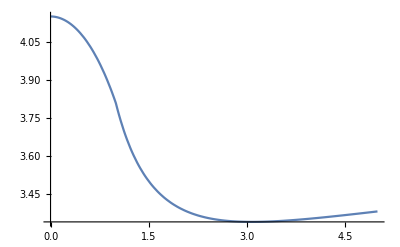

```mathematica
Plot[Piecewise[{{Pqq0DGLAP[kappa,0.3]/.CF->4/3,Abs[kappa]<1},{Pqq0ERBL[kappa,0.3]/.CF->4/3,Abs[kappa]>1}}],{kappa,0,5}]
```